```mathematica
y[t_]:= (2*Exp[3*t ]+ Exp[3])/(Exp[(3*t)/2] * (2+ Exp[3]));
u[t_]:= (2*  (Exp[3*t] - Exp[3]) )/(Exp[(3*t)/2] * (2+ Exp[3]));
lambda[t_]:=  -u[t];
```

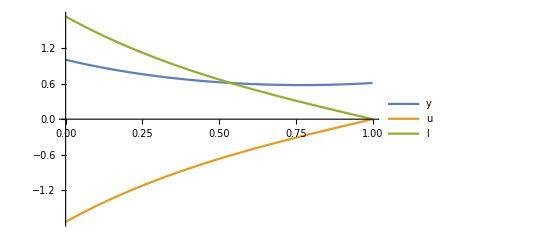

```mathematica
Plot[{y[t], u[t], lambda[t]}, {t,0,1}, PlotLegends->{"y", "u", "l"}]
```

```mathematica
g = y[t]^2 + 1/2 *  u[t]^2;
f = 1/2  *  y[t] + u[t];
```

```mathematica
D[y[t], {t,1}]- f//Simplify
D[lambda[t], {t,1}]  + 1/2* lambda[t] + 2* y[t]//Simplify
lambda[t] + u[t]//Simplify
```

0

0

0

```mathematica
Clear[u,sol]
u[x,t]=Sin[π x]
eq=D[T[x,t],t]-1/10*D[T[x,t],{x,2}]==u[x,t];
ic=T[x,0]==Sin[π x]+ Sin[2π x];
bc={T[0,t]==0,T[1,t]==0};
bc={T[0,t]==0,T[1,t]==0};
(*bc={Derivative[1,0][T][0,t]==0,Derivative[1,0][T][1,t]==0};*)
(*Sin[π x]*Sin[2 π*t]*)
sol=DSolveValue[{eq,ic,bc},T[x,t],{x,t}];
Plot3D[sol,{t,0,1},{x,0,1},AxesLabel->{t,x,T}]
```

Sin[π x]

-Graphics3D-

```mathematica
sol//Simplify
```

10 (ⅇ^(-(π^2 t)/10) (1/10-1/π^2)+1/π^2+1/5 ⅇ^(-(2 π^2 t)/5) Cos[π x]) Sin[π x]

```mathematica
u[x,t]
```

Sin[π x]